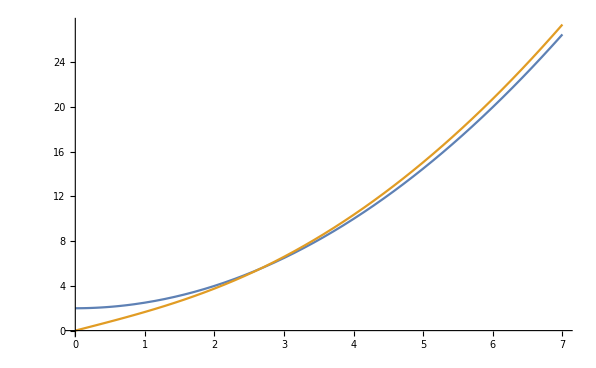

```mathematica
Plot[{z^2/2+2,Log[#[z]/(1-#[z])&@CDF[NormalDistribution[]]]},{z,0,7}]
```

```mathematica
Table[{z,z^2/2+2,Log[#[z]/(1-#[z])&@CDF[NormalDistribution[]]]},{z,0,7,.5}]//Grid
```

0. | 2. | 0.
0.5 | 2.125 | 0.806965
1. | 2.5 | 1.66827
1.5 | 3.125 | 2.6368
2. | 4. | 3.76017
2.5 | 5.125 | 5.07542
3. | 6.5 | 6.60638
3.5 | 8.125 | 8.36583
4. | 10. | 10.3601
4.5 | 12.125 | 12.5924
5. | 14.5 | 15.065
5.5 | 17.125 | 17.7794
6. | 20. | 20.7368
6.5 | 23.125 | 23.9381
7. | 26.5 | 27.3843